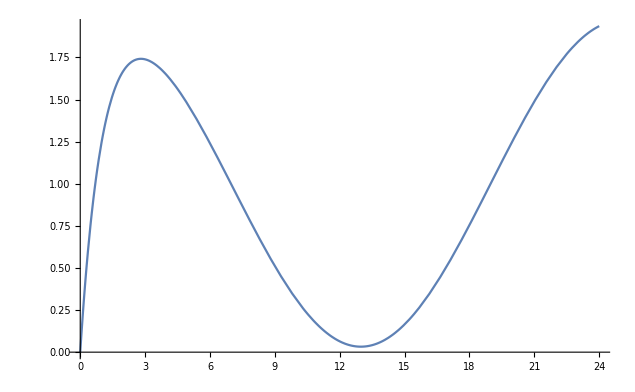

```mathematica
A=1;
theta=2*Pi/24;
w=0;
degradation=1;
x0=0;
s=NDSolve[{x'[t]==A*(1+Cos[theta*t-w])-degradation*x[t],x[0]==x0},x,{t,0,24}];
Plot[Evaluate[x[t]/. s],{t,0,24},PlotRange->All]
```